# Subspace recompilation for BCS Hamiltonian

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]*)
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
(*Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_gpu"];*)
```

### Modules

```mathematica
GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]
```

## BCS simulation

```mathematica
(* non-iteracting harmonic oscillator-type energy levels *)
ϵ=ω(#+0.5)&/@Range[0,4];
(* time-dependent coupling function *)
coupling[t_,g0_,gc_]:=ExpandAll[
(ArcTan[(t-t1)J/(ℏ Γ)]+π/2)(ArcTan[(t2-t)J/(ℏ Γ)]+π/2)(gc-g0)/π^2+g0
]
```

```mathematica
constants={
(* time start to quench and reverse. J is an arbitrary energy unit *)
t1->9 ℏ/J,
t2->18 ℏ/J,
(* initial coupling constant*)
Γ->0.1,
(* frequency *)
ω->5J/3
};
```

```mathematica
(* mean-field eigenvalues *)
Ej[ϵ_,Δ_]:=Sqrt[ϵ^2+Abs[Δ]^2]
(* superconducting gap *)
(*2/g=∑_k 1/Subscript[E, k] tanh[Subscript[E, k]/(2 Subscript[k, b] Temp)]*)
(* since we consider temperature Temp=0, tanh(∞)=1 *)
(* Superconducting gaps*)
Δ0=J;
Δc=2J;
```

```mathematica
g0=2 /Total[1/Ej[ϵ,Δ0]];
gc=2/ Total[1/Ej[ϵ,Δc]];
```

The entire BCS Hamiltonian

```mathematica
Hgaudin[q_,n_,ϵ_,g_]:=Total@Table[({Subscript[X, q],Subscript[Y, q],Subscript[Z, q]}.{Subscript[X, j],Subscript[Y, j],Subscript[Z, j]})/(2(ϵ[[q+1]]-ϵ[[j+1]])), {j,Complement[Range[0,n-1],{q}]}]+Subscript[Z, q]/g
```

```mathematica
HBCS[n_,ϵ_,τ_]:=With[{g=coupling[τ*ℏ/Δ0,g0,gc]/.constants},
SimplifyPaulis@Chop@ExpandAll[
Total@Table[
Simplify[(-g ϵ[[q+1]]+g^2/2)Hgaudin[q,n,ϵ,g]/Δ0/.constants,J>0]
,{q,n-1}]+
SimplifyPaulis@Chop@ExpandAll[SimplifyPaulis@Simplify[g^3/(4Δ0)*(Total@Table[Hgaudin[q,n,ϵ,g],{q,0,n-1}])^2/.constants,J>0]]
]
]
```

Constants

```mathematica
(*mean field-eigenvalues*)
ej=Simplify[Ej[ϵ,Δ0]/.constants,J>0];
(* |Subscript[v, j]|^2, |Subscript[u, j]|^2 *)
ujs=Simplify[0.5(1+ϵ/ej)/.constants,J>0];
vjs=Simplify[0.5(1-ϵ/ej)/.constants,J>0];
```

```mathematica
(*  
Subscript[u, j] 0-Subscript[v, j] 1;
Ry[θ]0=Cos[θ/2]0-Sin[θ/2]1 
 *)
θinit=2*ArcCos@Sqrt@ujs;
```

initial states and memory allocation

```mathematica
DestroyAllQuregs[]
{ψexact,ψinitexact}=CreateQuregs[5,2];
```

```mathematica
(*exact groundstate*)
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];
```

## Obtain the expression ⅇ^(-i δt H_BCS)

```mathematica
(* Medium resolution *)
τs=Sort@DeleteDuplicates@Chop@Join[{0.,4.,8.},Range[8.,20.,0.2],{20.,23.5,27}]
(* the timesteps *)
δτ=Table[τs[[i]]-τs[[i-1]],{i,2,Length@τs}];
PrependTo[δτ,0];
(*sanity check*)
And@@Table[τs[[i]]==Total[δτ[[#]]&/@Range[i]],{i,Length@τs}]
(*τ=t J/ℏ*)
```

{0,4.,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.,11.2,11.4,11.6,11.8,12.,12.2,12.4,12.6,12.8,13.,13.2,13.4,13.6,13.8,14.,14.2,14.4,14.6,14.8,15.,15.2,15.4,15.6,15.8,16.,16.2,16.4,16.6,16.8,17.,17.2,17.4,17.6,17.8,18.,18.2,18.4,18.6,18.8,19.,19.2,19.4,19.6,19.8,20.,23.5,27}

True

```mathematica
Length@τs
```

65

The time-dependent gap Δ is controlled through g(t). Definition of g(t) is here

```mathematica
(*τ=t J/ℏ*)
```

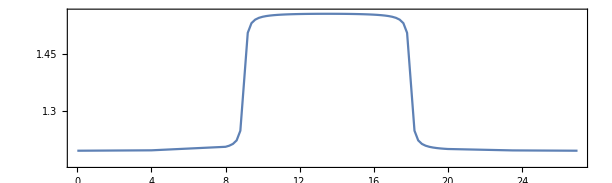

```mathematica
gvals=Simplify[(coupling[#*ℏ/Δ0,g0,gc]/Δ0&/@τs)//.constants,J>0];
ListPlot[Transpose@{τs,gvals},PlotRange->{1.16,1.56},Joined->True,AspectRatio->0.3,Frame->True,FrameTicks->{{Range[1,1.55,0.05],None},{Range[0,27,1],None}}]
```

```mathematica
τs[[2;;32]]
```

{4.,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.,11.2,11.4,11.6,11.8,12.,12.2,12.4,12.6,12.8,13.,13.2,13.4,13.6,13.8}

**** Compile @Tue 20 Dec 2022 12:17:44 τ=0; δ4. ****

Cycle 1@Tue 20 Dec 2022 12:27:14 completed with ngates=45, cost=3.4479412124310826e-6, at eval=1799

Cycle 2@Tue 20 Dec 2022 12:30:58 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 12:38:04 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=3.44794×10^-6

τ=4.; δ=4.; cost=2.37644×10^-6; ngates=45; runtime=24.6496 min

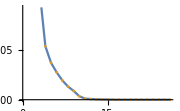

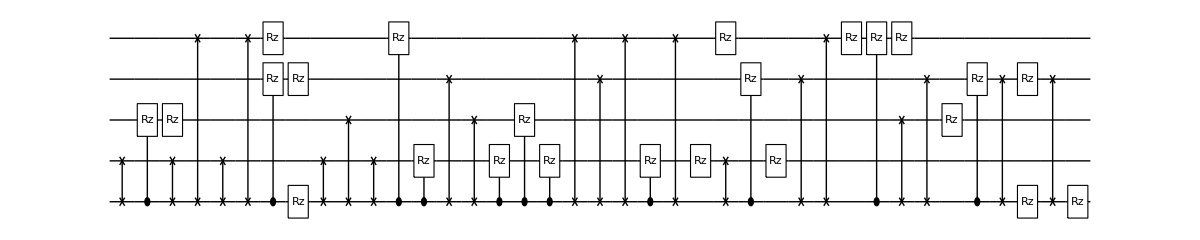

**** Compile @Tue 20 Dec 2022 12:42:23 τ=4.; δ4. ****

Cycle 1@Tue 20 Dec 2022 12:51:28 completed with ngates=43, cost=1.4328396381602104e-6, at eval=1917

Cycle 2@Tue 20 Dec 2022 12:55:05 adjust hyperparams, slowdown:True

ApplyCircuitDerivs::error: An equal number of variables and ouptut quregs must be passed.

τ=8.; δ=4.; cost=5.33731×10^-7; ngates=48; runtime=38.4038 min

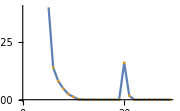

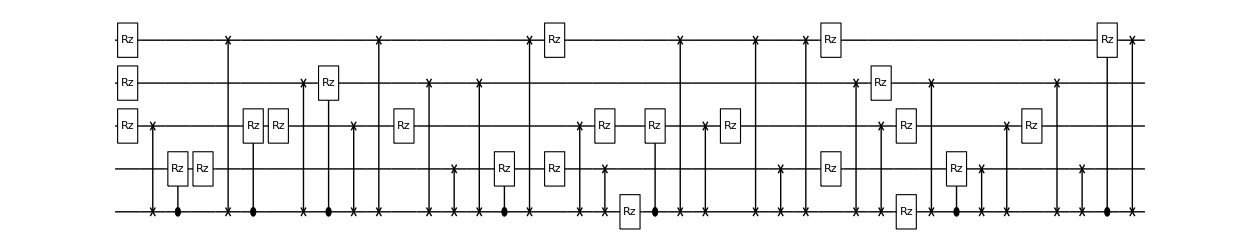

**** Compile @Tue 20 Dec 2022 13:20:48 τ=8.; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 13:27:08 completed with ngates=40, cost=0.00001555836775202213, at eval=1518

@cycle2, pathetic result.

Cycle 2@Tue 20 Dec 2022 13:29:54 adjust hyperparams, slowdown:True

ApplyCircuitDerivs::error: An equal number of variables and ouptut quregs must be passed.

Cycle 3@Tue 20 Dec 2022 13:41:48 completed with ngates=55, cost=2.1667246398182627e-6, at eval=3767

Cycle 4@Tue 20 Dec 2022 13:49:23 adjust hyperparams, slowdown:True

τ=8.2; δ=0.2; cost=5.9649×10^-7; ngates=63; runtime=56.6652 min

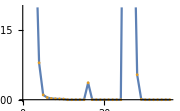

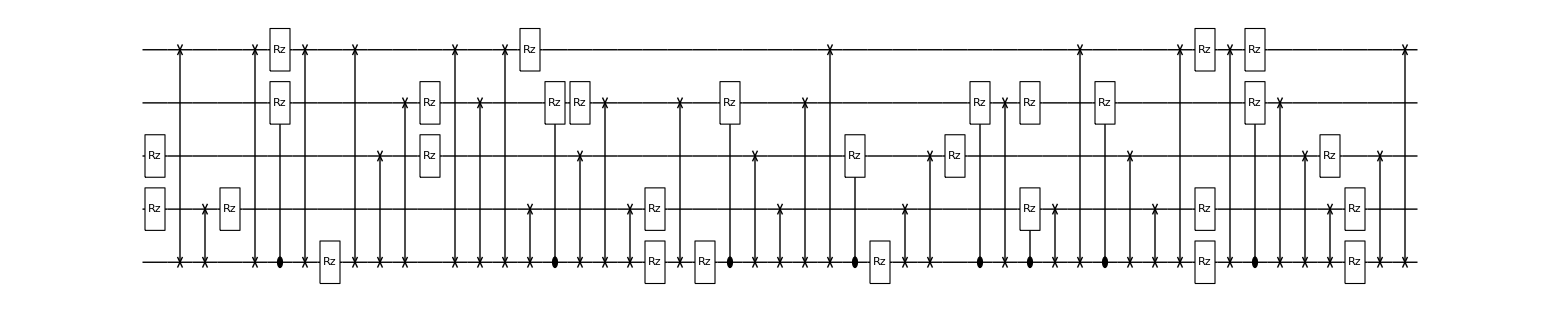

**** Compile @Tue 20 Dec 2022 14:17:28 τ=8.2; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 14:23:19 completed with ngates=40, cost=0.000022053402970789726, at eval=1511

Cycle 2@Tue 20 Dec 2022 14:26:13 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 14:39:08 completed with ngates=63, cost=2.3956853338891193e-6, at eval=3830

Cycle 4@Tue 20 Dec 2022 14:47:25 adjust hyperparams, slowdown:True

ApplyCircuitDerivs::error: An equal number of variables and ouptut quregs must be passed.

General::stop: Further output of ApplyCircuitDerivs::error will be suppressed during this calculation.

τ=8.4; δ=0.2; cost=4.51734×10^-7; ngates=54; runtime=63.0813 min

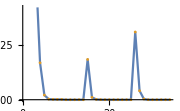

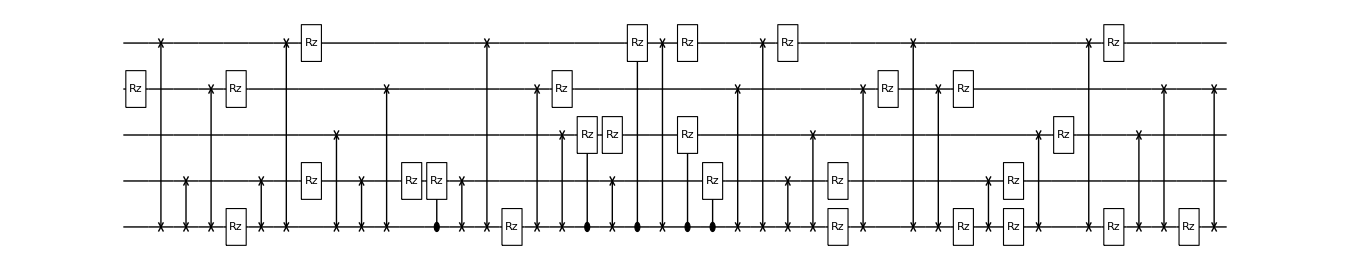

**** Compile @Tue 20 Dec 2022 15:20:33 τ=8.4; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 15:27:10 completed with ngates=42, cost=0.00004088296498694355, at eval=1494

Cycle 2@Tue 20 Dec 2022 15:35:15 completed with ngates=45, cost=0.000012988867765906242, at eval=3284

Cycle 3@Tue 20 Dec 2022 15:38:27 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 15:44:41 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000129889

τ=8.6; δ=0.2; cost=0.0000129889; ngates=45; runtime=25.5098 min

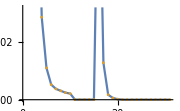

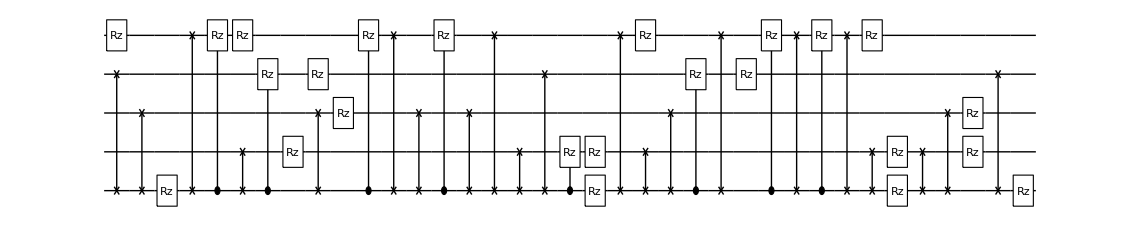

**** Compile @Tue 20 Dec 2022 15:46:04 τ=8.6; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 15:52:47 completed with ngates=47, cost=0.000020102417606859824, at eval=1590

Cycle 2@Tue 20 Dec 2022 16:00:41 completed with ngates=58, cost=5.639517549838047e-6, at eval=3122

Cycle 3@Tue 20 Dec 2022 16:04:18 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 16:11:49 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=5.63952×10^-6

τ=8.8; δ=0.2; cost=4.58547×10^-6; ngates=58; runtime=28.258 min

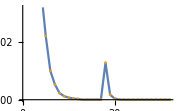

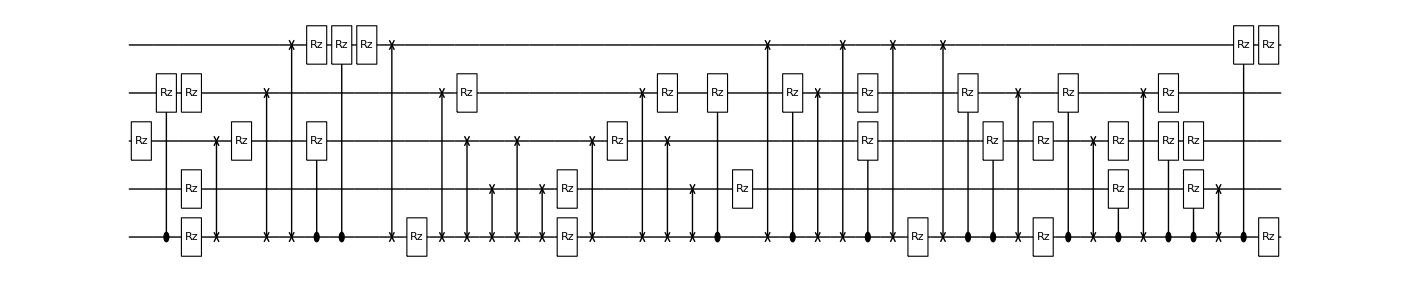

**** Compile @Tue 20 Dec 2022 16:14:19 τ=8.8; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 16:21:21 completed with ngates=38, cost=0.000027820776400178104, at eval=1606

Cycle 2@Tue 20 Dec 2022 16:28:56 completed with ngates=50, cost=2.016865055964878e-6, at eval=3077

Cycle 3@Tue 20 Dec 2022 16:32:33 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 16:39:18 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=2.01687×10^-6

τ=9.; δ=0.2; cost=2.01687×10^-6; ngates=50; runtime=27.2216 min

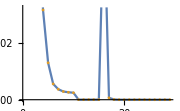

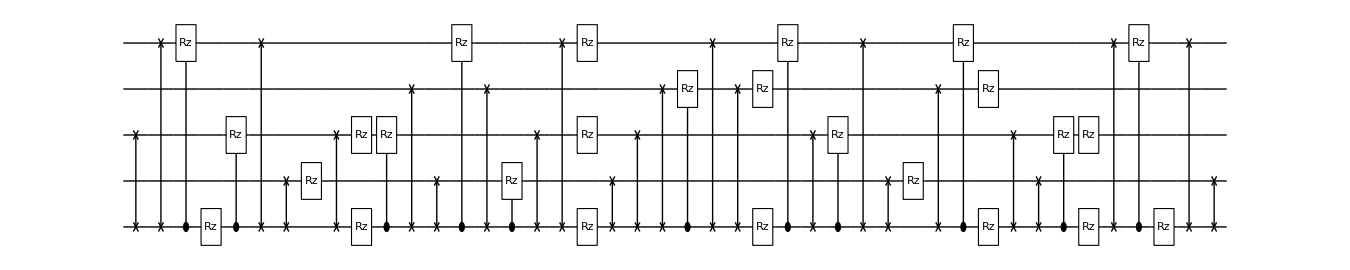

**** Compile @Tue 20 Dec 2022 16:41:33 τ=9.; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 16:48:13 completed with ngates=43, cost=9.839291121194194e-6, at eval=1594

Cycle 2@Tue 20 Dec 2022 16:51:10 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 16:56:40 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=9.83929×10^-6

τ=9.2; δ=0.2; cost=9.83929×10^-6; ngates=43; runtime=16.2873 min

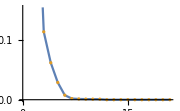

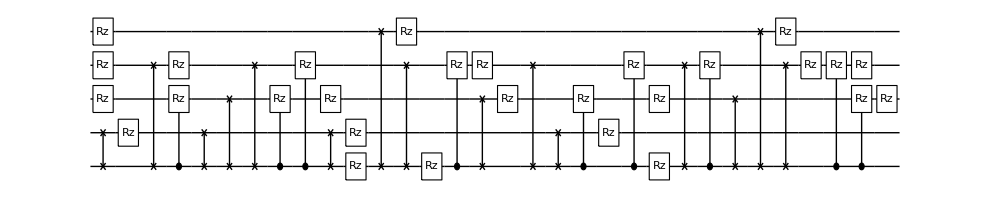

**** Compile @Tue 20 Dec 2022 16:57:50 τ=9.2; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 17:03:06 completed with ngates=33, cost=0.00010429647265719488, at eval=1423

Cycle 2@Tue 20 Dec 2022 17:07:23 completed with ngates=34, cost=0.000012922428091699523, at eval=2660

Cycle 3@Tue 20 Dec 2022 17:09:50 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 17:15:00 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000129224

τ=9.4; δ=0.2; cost=0.0000116573; ngates=34; runtime=17.8286 min

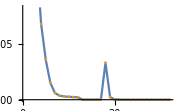

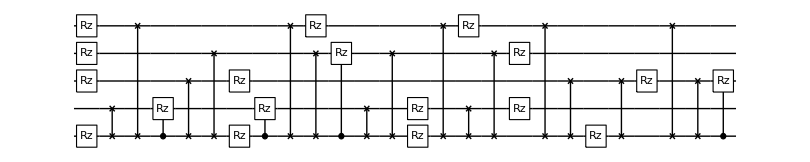

**** Compile @Tue 20 Dec 2022 17:15:47 τ=9.4; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 17:23:26 completed with ngates=44, cost=0.000027068856920942075, at eval=2019

Cycle 2@Tue 20 Dec 2022 17:26:19 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 17:42:30 completed with ngates=50, cost=5.746664965999848e-6, at eval=5201

Cycle 4@Tue 20 Dec 2022 17:49:11 adjust hyperparams, slowdown:True

Cycle 5@Tue 20 Dec 2022 18:26:35 completed with ngates=73, cost=6.68101179268632e-7, at eval=8635

τ=9.6; δ=0.2; cost=6.68101×10^-7; ngates=73; runtime=86.121 min

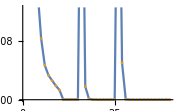

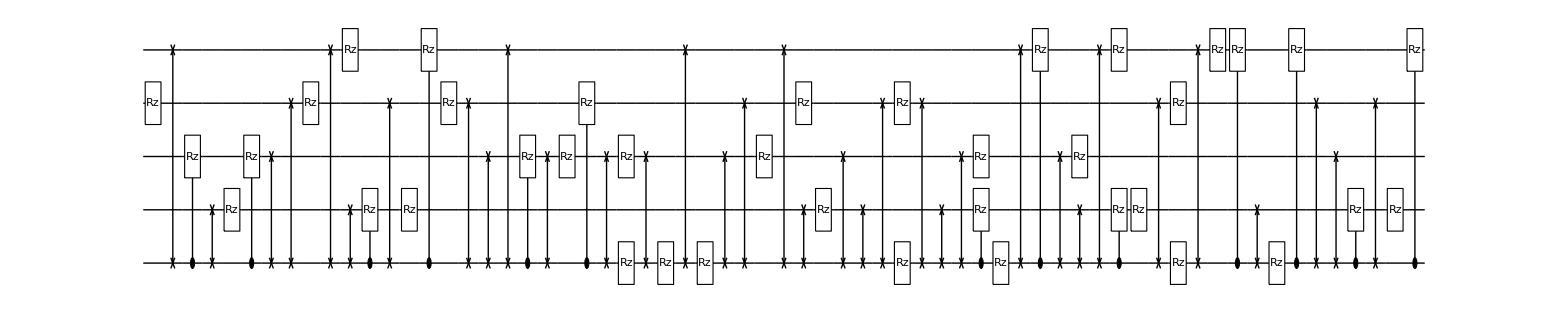

**** Compile @Tue 20 Dec 2022 18:42:01 τ=9.6; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 18:49:48 completed with ngates=44, cost=0.000020987891708901252, at eval=2001

Cycle 2@Tue 20 Dec 2022 18:52:36 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 18:58:02 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000209879

τ=9.8; δ=0.2; cost=0.0000209879; ngates=44; runtime=17.245 min

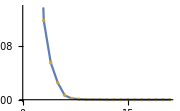

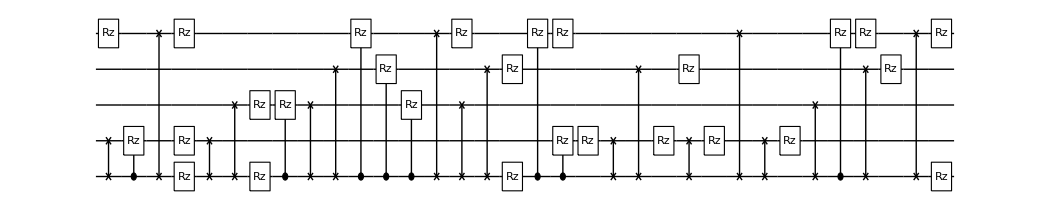

**** Compile @Tue 20 Dec 2022 18:59:22 τ=9.8; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 19:05:55 completed with ngates=43, cost=4.975382359218017e-6, at eval=1648

Cycle 2@Tue 20 Dec 2022 19:08:36 adjust hyperparams, slowdown:True

@cycle3, pathetic result.

Cycle 3@Tue 20 Dec 2022 19:13:57 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=4.97538×10^-6

τ=10.; δ=0.2; cost=4.97538×10^-6; ngates=43; runtime=15.8998 min

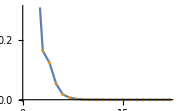

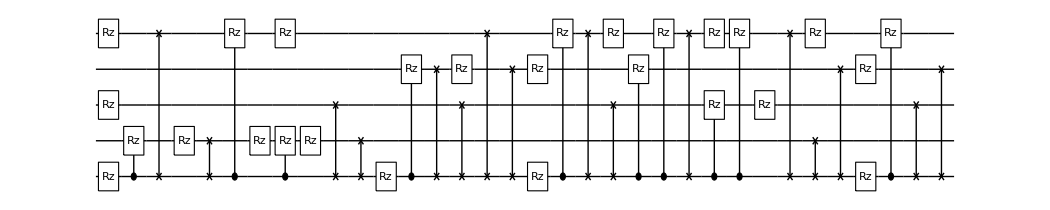

**** Compile @Tue 20 Dec 2022 19:15:23 τ=10.; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 19:23:09 completed with ngates=32, cost=0.00011962820390798434, at eval=2376

Cycle 2@Tue 20 Dec 2022 19:28:13 completed with ngates=40, cost=0.000021016705151755133, at eval=3850

Cycle 3@Tue 20 Dec 2022 19:35:20 completed with ngates=51, cost=1.4135092233358293e-6, at eval=5372

Cycle 4@Tue 20 Dec 2022 19:38:41 adjust hyperparams, slowdown:True

Cycle 5@Tue 20 Dec 2022 19:45:12 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=1.41351×10^-6

τ=10.2; δ=0.2; cost=9.37794×10^-7; ngates=51; runtime=31.9643 min

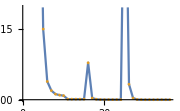

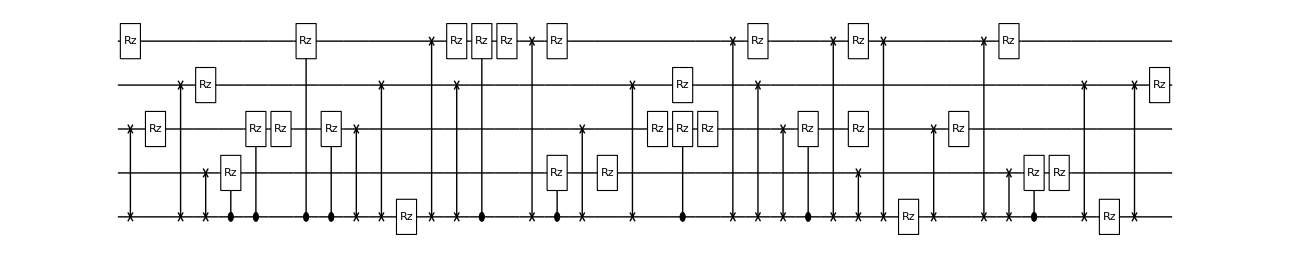

**** Compile @Tue 20 Dec 2022 19:47:27 τ=10.2; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 19:53:36 completed with ngates=36, cost=0.000010744347534341614, at eval=1565

Cycle 2@Tue 20 Dec 2022 19:56:20 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 20:01:25 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000101041

τ=10.4; δ=0.2; cost=8.12308×10^-6; ngates=36; runtime=14.7647 min

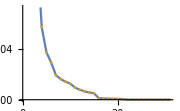

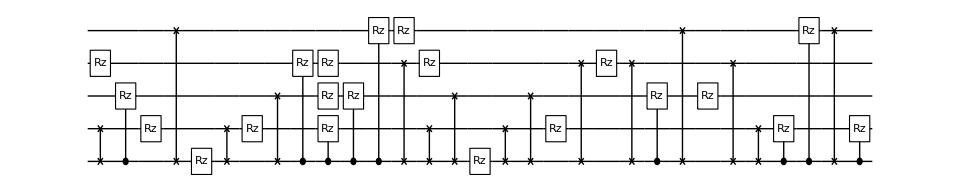

**** Compile @Tue 20 Dec 2022 20:02:20 τ=10.4; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 20:10:36 completed with ngates=52, cost=2.087831588282185e-6, at eval=1752

Cycle 2@Tue 20 Dec 2022 20:14:23 adjust hyperparams, slowdown:True

τ=10.6; δ=0.2; cost=6.00476×10^-7; ngates=81; runtime=26.3901 min

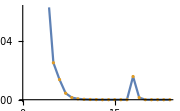

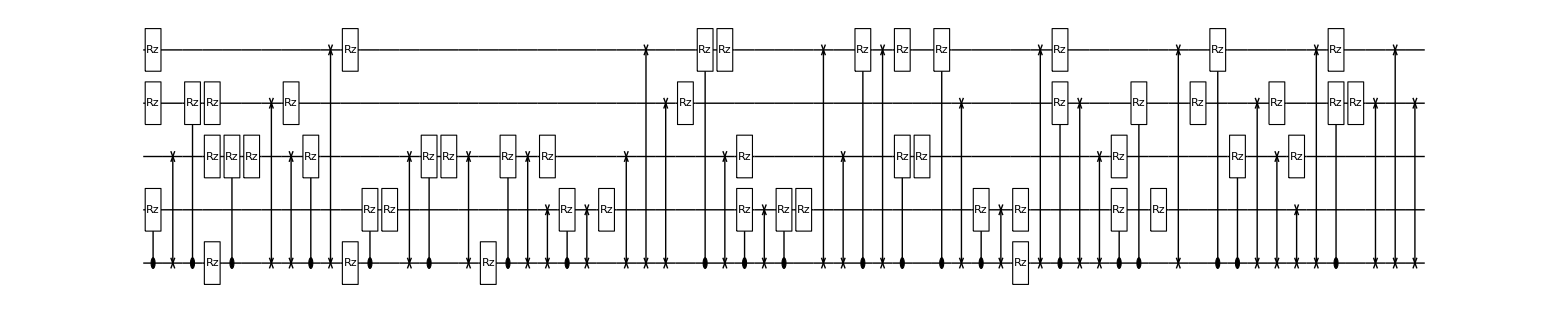

**** Compile @Tue 20 Dec 2022 20:28:50 τ=10.6; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 20:34:33 completed with ngates=37, cost=0.00001915127175455833, at eval=1471

Cycle 2@Tue 20 Dec 2022 20:37:09 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 20:49:46 completed with ngates=50, cost=4.166216333589823e-6, at eval=4148

@cycle4, pathetic result.

Cycle 4@Tue 20 Dec 2022 20:56:18 adjust hyperparams, slowdown:True

τ=10.8; δ=0.2; cost=6.65348×10^-7; ngates=59; runtime=48.8448 min

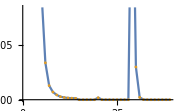

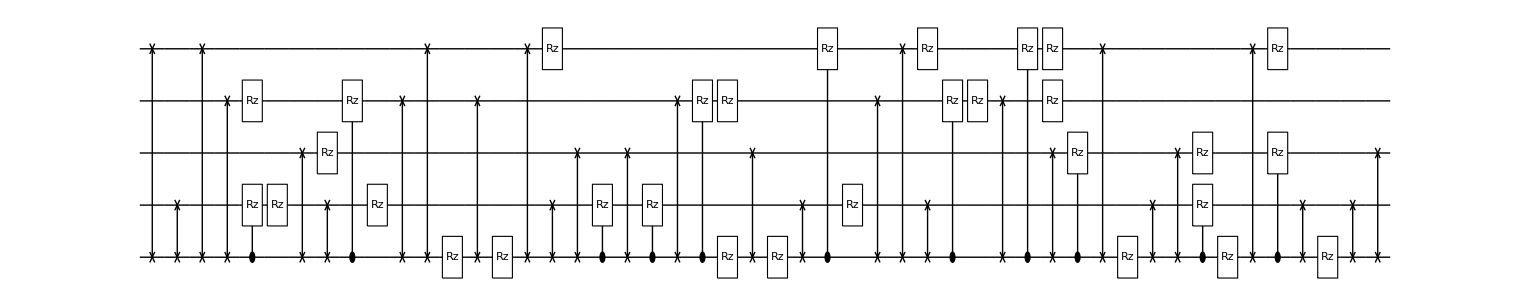

**** Compile @Tue 20 Dec 2022 21:17:48 τ=10.8; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 21:23:33 completed with ngates=38, cost=0.000025255945983015948, at eval=1545

Cycle 2@Tue 20 Dec 2022 21:26:03 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 21:30:59 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000252559

τ=11.; δ=0.2; cost=0.0000243024; ngates=38; runtime=13.9988 min

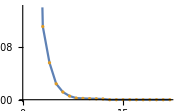

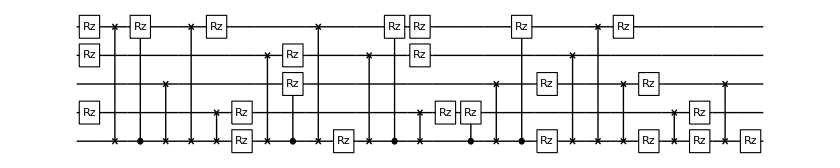

**** Compile @Tue 20 Dec 2022 21:31:54 τ=11.; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 21:38:20 completed with ngates=36, cost=0.000029654910243648303, at eval=1786

Cycle 2@Tue 20 Dec 2022 21:40:49 adjust hyperparams, slowdown:True

@cycle3, pathetic result.

Cycle 3@Tue 20 Dec 2022 21:45:46 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000296549

τ=11.2; δ=0.2; cost=0.0000296549; ngates=36; runtime=14.533 min

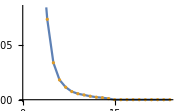

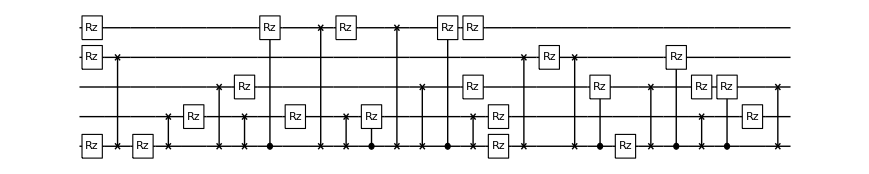

**** Compile @Tue 20 Dec 2022 21:46:33 τ=11.2; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 21:53:25 completed with ngates=43, cost=3.271797228587836e-6, at eval=1589

Cycle 2@Tue 20 Dec 2022 21:56:28 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 22:02:14 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=3.2718×10^-6

τ=11.4; δ=0.2; cost=2.71384×10^-6; ngates=43; runtime=16.8669 min

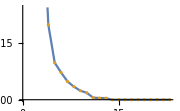

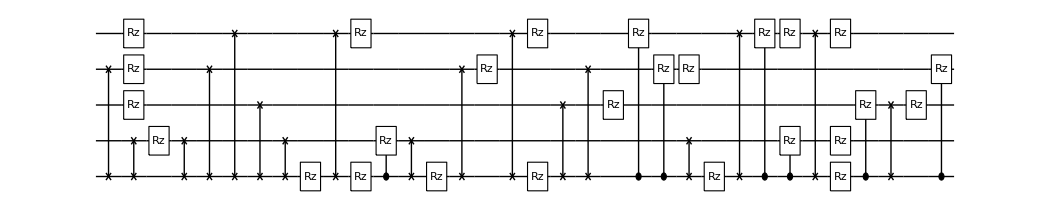

**** Compile @Tue 20 Dec 2022 22:03:32 τ=11.4; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 22:10:06 completed with ngates=43, cost=0.000020558730088882093, at eval=1551

Cycle 2@Tue 20 Dec 2022 22:13:06 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 22:31:33 completed with ngates=60, cost=9.19621404138482e-7, at eval=4490

τ=11.6; δ=0.2; cost=9.19621×10^-7; ngates=60; runtime=31.2526 min

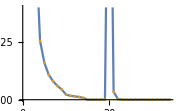

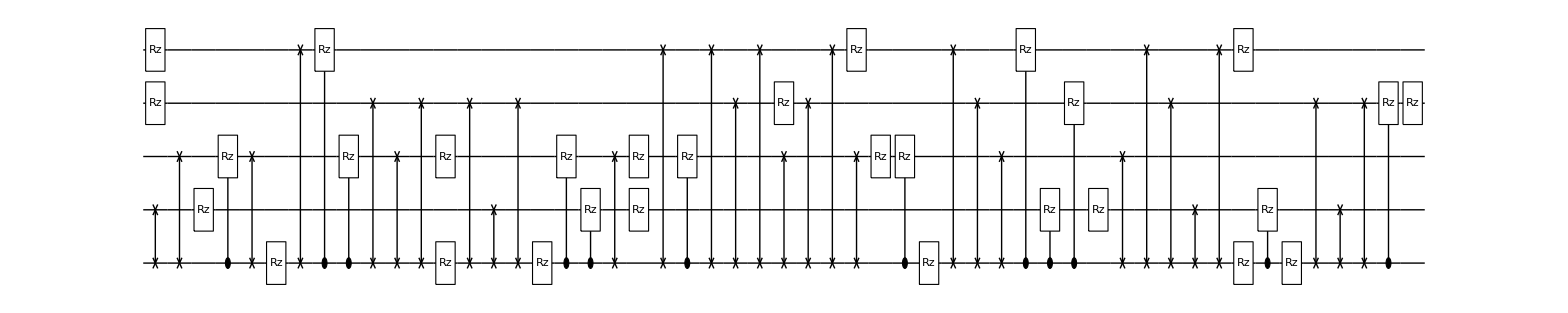

**** Compile @Tue 20 Dec 2022 22:34:54 τ=11.6; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 22:40:42 completed with ngates=34, cost=0.000024666560009323213, at eval=1492

Cycle 2@Tue 20 Dec 2022 22:43:15 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 22:48:15 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000246666

τ=11.8; δ=0.2; cost=0.0000246666; ngates=34; runtime=13.9711 min

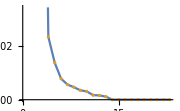

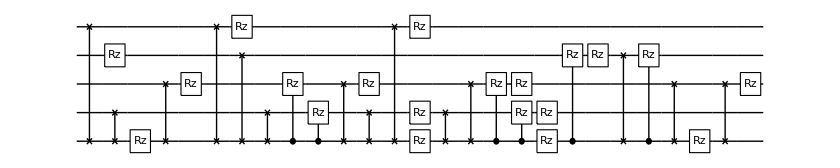

**** Compile @Tue 20 Dec 2022 22:49:00 τ=11.8; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 22:56:00 completed with ngates=45, cost=3.502900984830859e-6, at eval=1666

Cycle 2@Tue 20 Dec 2022 22:58:57 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 23:04:56 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=3.5029×10^-6

τ=12.; δ=0.2; cost=3.5029×10^-6; ngates=45; runtime=17.2544 min

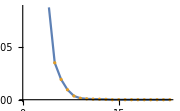

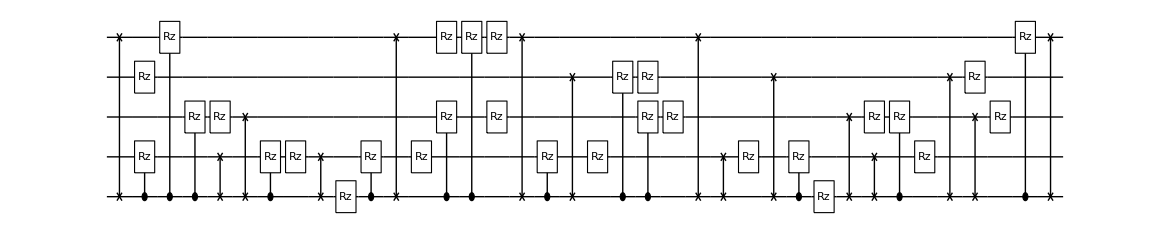

**** Compile @Tue 20 Dec 2022 23:06:22 τ=12.; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 23:12:03 completed with ngates=35, cost=0.00015495221830830186, at eval=1628

Cycle 2@Tue 20 Dec 2022 23:17:11 completed with ngates=34, cost=0.000028823197591121286, at eval=3096

Cycle 3@Tue 20 Dec 2022 23:19:47 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 23:24:59 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000288232

τ=12.2; δ=0.2; cost=0.0000253152; ngates=34; runtime=19.6079 min

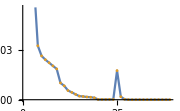

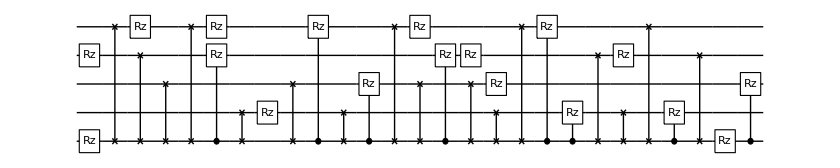

**** Compile @Tue 20 Dec 2022 23:26:05 τ=12.2; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 23:31:39 completed with ngates=37, cost=4.641381149306234e-6, at eval=1484

Cycle 2@Tue 20 Dec 2022 23:34:22 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 23:39:25 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=4.64138×10^-6

τ=12.4; δ=0.2; cost=4.64138×10^-6; ngates=37; runtime=14.0788 min

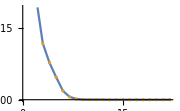

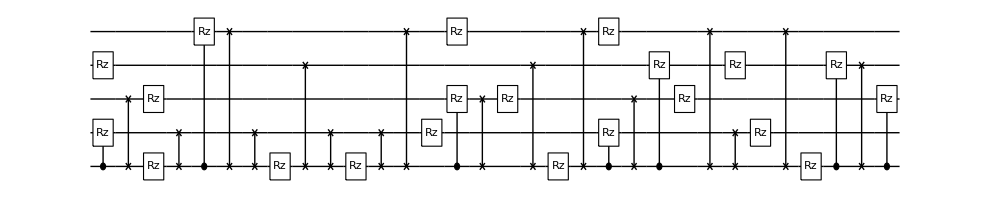

**** Compile @Tue 20 Dec 2022 23:40:17 τ=12.4; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 23:46:41 completed with ngates=32, cost=0.00003315351392996213, at eval=1982

Cycle 2@Tue 20 Dec 2022 23:48:45 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 23:58:28 completed with ngates=43, cost=3.5935131988962254e-6, at eval=4584

Cycle 4@Wed 21 Dec 2022 00:04:16 adjust hyperparams, slowdown:True

τ=12.6; δ=0.2; cost=2.99354×10^-7; ngates=57; runtime=45.2403 min

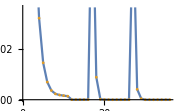

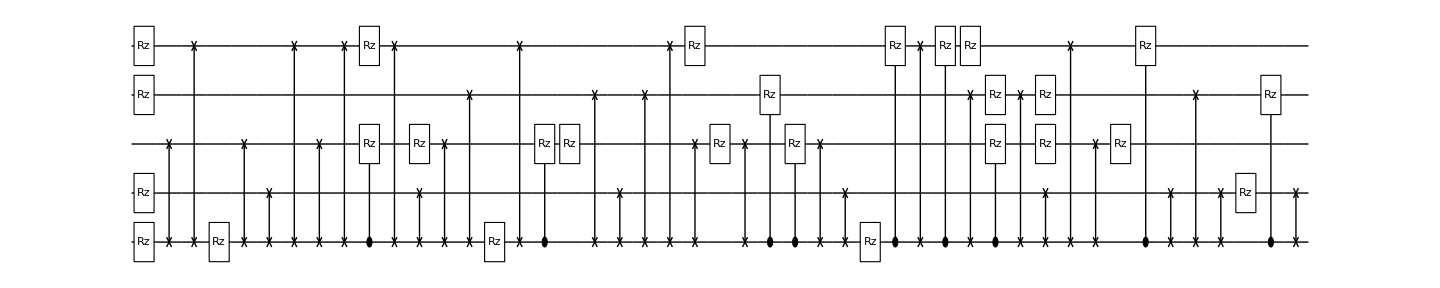

**** Compile @Wed 21 Dec 2022 00:25:38 τ=12.6; δ0.2 ****

Cycle 1@Wed 21 Dec 2022 00:30:18 completed with ngates=27, cost=0.0002940640086065427, at eval=1445

Cycle 2@Wed 21 Dec 2022 00:33:43 completed with ngates=31, cost=0.000029226515550262455, at eval=2765

Cycle 3@Wed 21 Dec 2022 00:35:54 adjust hyperparams, slowdown:True

Cycle 4@Wed 21 Dec 2022 00:43:55 completed with ngates=45, cost=5.1288489351097866e-6, at eval=4866

Cycle 5@Wed 21 Dec 2022 00:49:21 adjust hyperparams, slowdown:True

Cycle 6@Wed 21 Dec 2022 01:23:00 completed with ngates=68, cost=7.416784281177868e-7, at eval=8345

τ=12.8; δ=0.2; cost=7.41678×10^-7; ngates=68; runtime=61.8851 min

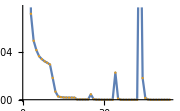

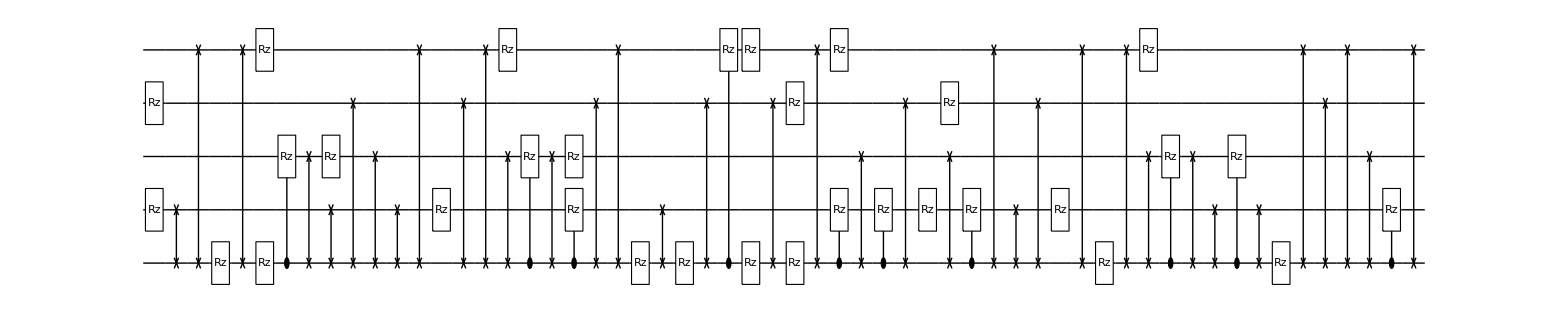

**** Compile @Wed 21 Dec 2022 01:27:37 τ=12.8; δ0.2 ****

Cycle 1@Wed 21 Dec 2022 01:36:02 completed with ngates=43, cost=1.6707234816726313e-6, at eval=2175

Cycle 2@Wed 21 Dec 2022 01:38:53 adjust hyperparams, slowdown:True

Cycle 3@Wed 21 Dec 2022 01:44:22 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=1.67072×10^-6

τ=13.; δ=0.2; cost=1.67072×10^-6; ngates=43; runtime=17.8694 min

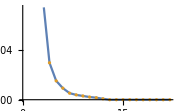

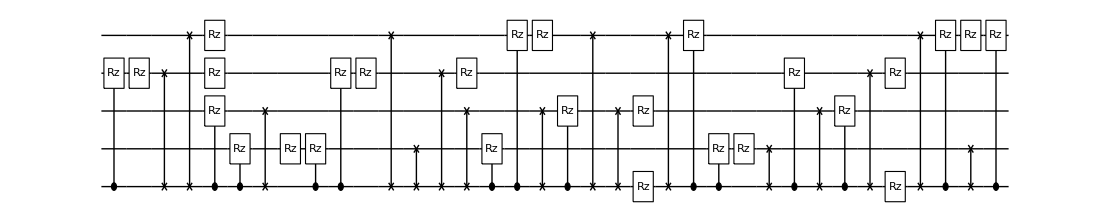

**** Compile @Wed 21 Dec 2022 01:45:36 τ=13.; δ0.2 ****

Cycle 1@Wed 21 Dec 2022 01:51:30 completed with ngates=37, cost=2.9634854765703267e-6, at eval=1528

Cycle 2@Wed 21 Dec 2022 01:53:59 adjust hyperparams, slowdown:True

Cycle 3@Wed 21 Dec 2022 01:58:58 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=2.96349×10^-6

τ=13.2; δ=0.2; cost=2.89794×10^-6; ngates=37; runtime=14.2701 min

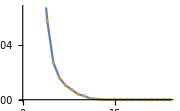

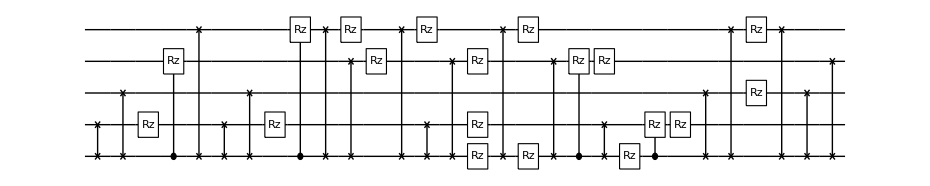

**** Compile @Wed 21 Dec 2022 01:59:59 τ=13.2; δ0.2 ****

Cycle 1@Wed 21 Dec 2022 02:05:00 completed with ngates=31, cost=0.00008085919228628669, at eval=1431

Cycle 2@Wed 21 Dec 2022 02:07:02 adjust hyperparams, slowdown:True

Cycle 3@Wed 21 Dec 2022 02:15:40 completed with ngates=50, cost=0.000016279517714767877, at eval=3561

Cycle 4@Wed 21 Dec 2022 02:22:15 adjust hyperparams, slowdown:True

Cycle 5@Wed 21 Dec 2022 02:52:57 completed with ngates=67, cost=1.3860249129526991e-6, at eval=6892

τ=13.4; δ=0.2; cost=6.94127×10^-7; ngates=67; runtime=56.9385 min

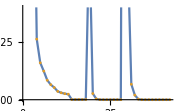

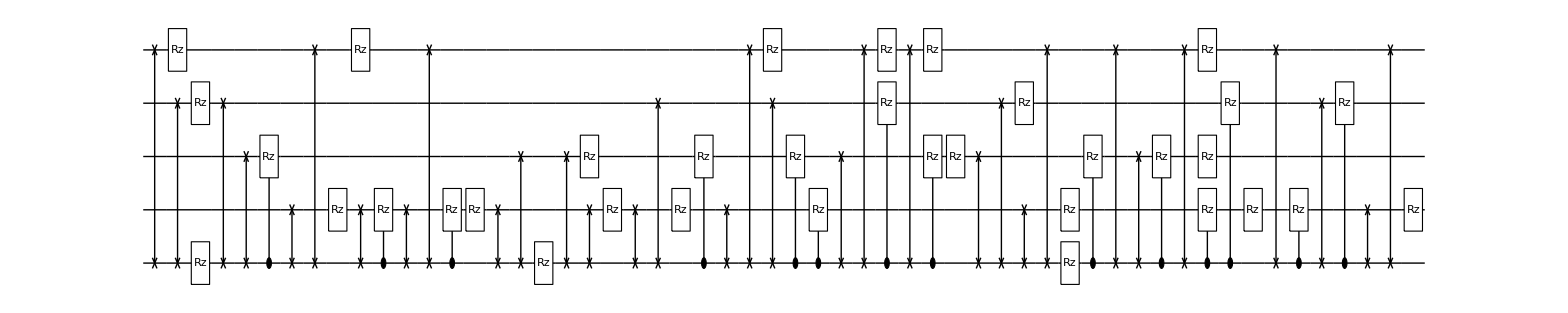

**** Compile @Wed 21 Dec 2022 02:57:02 τ=13.4; δ0.2 ****

Cycle 1@Wed 21 Dec 2022 03:03:02 completed with ngates=34, cost=0.00005291926310335704, at eval=1680

Cycle 2@Wed 21 Dec 2022 03:05:30 adjust hyperparams, slowdown:True

Cycle 3@Wed 21 Dec 2022 03:10:27 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000519906

τ=13.6; δ=0.2; cost=0.000038914; ngates=34; runtime=14.0486 min

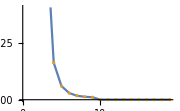

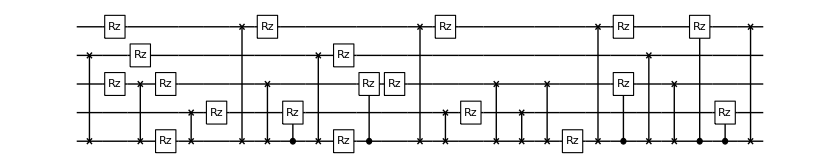

**** Compile @Wed 21 Dec 2022 03:11:12 τ=13.6; δ0.2 ****

Cycle 1@Wed 21 Dec 2022 03:18:24 completed with ngates=45, cost=6.282098595877805e-6, at eval=1628

Cycle 2@Wed 21 Dec 2022 03:21:38 adjust hyperparams, slowdown:True

Cycle 3@Wed 21 Dec 2022 03:27:46 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=6.2821×10^-6

τ=13.8; δ=0.2; cost=5.6177×10^-6; ngates=45; runtime=18.0052 min

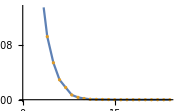

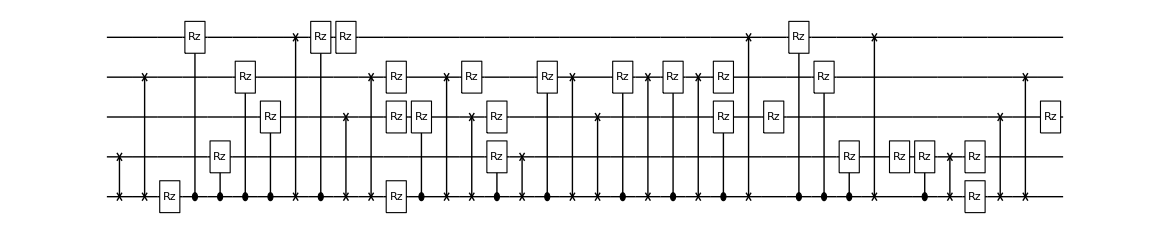

```mathematica
τ=0;
bcscompilecss1={};
Table[
Print["**** Compile @",DateString[]," τ=",τ, "; δ",δ," ****"];
hbcsmat=Chop@MatrixExp[-ⅈ *δ*CalcPauliStringMatrix[HBCS[5,ϵ,τ]]]; 
DestroyAllQuregs[];
τ+=δ;
conf=DefaultConfig[5,{1,2,4,8,16}];
res=CJRecompile[5,hbcsmat,conf];
AppendTo[bcscompilecss1,{τ,δ,res}];

DumpSave["bcscompilecss1.mx",bcscompilecss1];
{time,Ecur,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elimmerge,elimbfsmall,elimmetov,elimbf}=res;
Print["τ=",τ, "; δ=",δ,"; cost=",Ecur,"; ngates=",Length@ansatz,"; runtime=",time];
Print@ListPlot[{Elist,Elist},Joined->{True,False},ImageSize->Small];
Print@DrawCircuit[ansatz/.CustomGatesDraw,5];
,{δ,δτ[[2;;32]]}];
```

```mathematica
rexactot2<<rexactot2.mx
```

Null rexactot2

The matrixExp vs compiled

```mathematica
(*initialisation*)
{ψexact,ψinitexact}=CreateQuregs[5,2];
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];
```

```mathematica
CloneQureg[ψexact,ψinitexact];
rexactcomp={{0,1}};
Table[
{τ,δ,res}=comp;
ApplyCircuit[ψexact,res[[4]]/.CustomGatesDefinitions/.res[[5]]];
AppendTo[rexactcomp,{τ,CalcFidelity[ψexact,ψinitexact]}]
,{comp, bcscompilecss}];
```

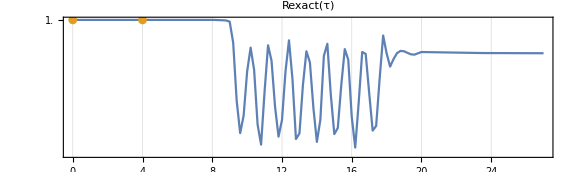

```mathematica
ListPlot[{rexactot2,rexactcomp},Joined->{True,False},PlotTheme->"Detailed",AspectRatio->0.3,PlotLabel->"Rexact(τ)",ImageSize->Large,FrameTicks->{{Range[1,1.55,0.05],None},{Automatic,None}}]
```